```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* constantes físicas *)
Clear[hbar,e,massae,eps0]
hbar=1.0545718 10^-34;(* constante de Planck *)
e=1.6021766 10^-19 ;(* carga do eletron *)
massae=9.10938356 10^-31 ;(* masa do eletron *)
eps0=8.8541878176 10^-12;(* constante de permissividade do vácuo *)
```

```mathematica
Clear[deltaEc,deltaEv,me,mh,ctedielet,camadas,a]
(* os seguintes dados são para nanocristais de Perovskita *)
deltaEc=1.25e; (* altura do poco do eletron *)
deltaEv=1.45e; (* altura do poco do buraco *)
me=massae.15 ;(* massa efetiva do eletron *)
mh=massae.14 ;(* massa efetiva do buraco *)
ctedielet=4.96; (* cte dieletrica *)
camadas=5; (* numero de camadas *)
a=camadas.59 10^-9/2;(* raio do quantum dot *)
Print[2a]
```

2.95×10^-9

```mathematica
Clear[mi,eps]
(* outras constântes *)
mi=1/(1/me+1/mh); (* mu_perp *)
eps=ctedielet eps0; (* permissividade do material *)
```

```mathematica
Clear[keFunc,kappaeFunc,fTranscEFunc,EchuteE,khFunc,kappahFunc,fTranscHFunc,EchuteH,epsE,E0e,E0h]
epsE=e 10^-6;(* epsilon de energia *)
keFunc[energia_]:=Sqrt[2me energia]/hbar(* função k do elétron *)
kappaeFunc[energia_]:=Sqrt[2me(deltaEc-energia)]/hbar(* função kappa do elétron *)
fTranscEFunc[energia_]:=kappaeFunc[energia]Tan[keFunc[energia]a]+keFunc[energia] (* eq. transcendental do elétron *)
E0e=(Pi hbar/a)^2/8/me;(* ponto em que há a primeira divergência de fTranscEFunc *)
EchuteE[]:=(For[Ei=E0e+epsE,Ei<deltaEc,Ei+=deltaEc/1000,
If[fTranscEFunc[Ei]fTranscEFunc[Ei+deltaEc/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscEFunc *)
khFunc[energia_]:=Sqrt[2mh energia]/hbar(* função k do buraco *)
kappahFunc[energia_]:=Sqrt[2mh(deltaEv-energia)]/hbar(* função kappa do buraco *)
fTranscHFunc[energia_]:=kappahFunc[energia]Tan[khFunc[energia]a]+khFunc[energia] (* eq. transcendental do buraco *)
E0h=(Pi hbar/a)^2/8/mh;(* ponto em que há a primeira divergência de fTranscHFunc *)
EchuteH[]:=(For[Ei=E0h+epsE,Ei<deltaEv,Ei+=deltaEv/1000,
If[fTranscHFunc[Ei]fTranscHFunc[Ei+deltaEv/1000 ]<0,Break[]]
];
Return[Ei])(* retorna um valor aproximado para o valor de energia correspondente a primeira raiz de fTranscHFunc *)
```

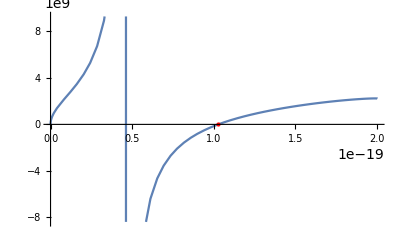

```mathematica
Clear[Ee,ke,kappae]
Ee=energia/.FindRoot[fTranscEFunc[energia],{energia,EchuteE[]}];
ke=keFunc[Ee];
kappae=kappaeFunc[Ee];

Show[Plot[fTranscEFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Ee,fTranscEFunc[Ee]}]}]]
```

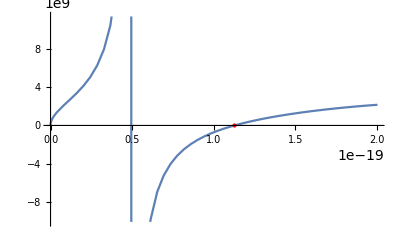

```mathematica
Clear[Eh,kh,kappah]
Eh=energia/.FindRoot[fTranscHFunc[energia],{energia,EchuteH[]}];
kh=khFunc[Eh];
kappah=kappahFunc[Eh];

Show[Plot[fTranscHFunc[energia],{energia,0,deltaEc}],Graphics[{PointSize[Medium],Red,Point[{Eh,fTranscHFunc[Eh]}]}]]
```

```mathematica
Clear[psieAux,psihAux]
(* função de onda analítica do elétron em função da distância x *)
psieAux[x_]:=Piecewise[{{1,x==0},{Sin[ke x]/ke/x,0<x<a},{Exp[kappae a]Sin[ke a]Exp[-kappae x]/ke/x,x>a}}]
(* função de onda analítica do buraco em função da distância x *)
psihAux[x_]:=Piecewise[{{1,x==0},{Sin[kh x]/kh/x,0≤x<a},{Exp[kappah a]Sin[kh a]Exp[-kappah x]/kh/x,x>a}}]
```

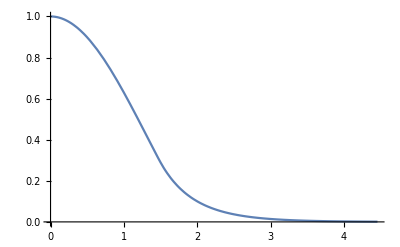

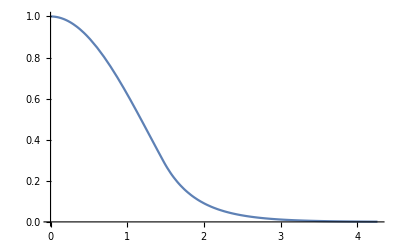

```mathematica
Clear[epsPsi,fTranscPsiE,fTranscPsiH]
(* vou considerar que as funções de onda são nulas para x ≥ L e para x ≤ L farei interpolação por motivos de otimização. 
O valor de L é tomado como sendo o ponto no qual a função de onda tem valor epsPsi *)
epsPsi=10^-3;
fTranscPsiE[x_]:=psieAux[x]-epsPsi
fTranscPsiH[x_]:=psihAux[x]-epsPsi
Le=r/.FindRoot[fTranscPsiE[r],{r,a}];(* L do elétron *)
Lh=r/.FindRoot[fTranscPsiH[r],{r,a}];(* L do buraco *)
(* interpolação da função de onda do elétron em função da distância x *)
psie=Interpolation[Table[{x,psieAux[x]},{x,0,Le,Le/100}]];
(* interpolação da função de onda do buraco em função da distância x *)
psih=Interpolation[Table[{x,psihAux[x]},{x,0,Lh,Lh/100}]];
Plot[psie[r],{r,0,Le}]
Plot[psih[r],{r,0,Lh}]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.7161×10^-54 and 1.38801×10^-58 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.46199×10^-37 and 6.9408×10^-39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.45875×10^-37 and 7.17797×10^-39 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

Part::partw: Part 2 of {-261.97} does not exist.

Part::partw: Part 3 of {-261.97} does not exist.

Part::partw: Part 4 of {-261.97} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

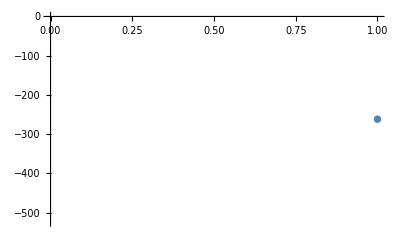

```mathematica
Clear[d,A,B,c,Es,out,nome]
(* o ponto de mínimo é procurado em um range de lambda entre [lambIni, lambFin] com lambN pontos.
Os integrandos foram calculados em um outro arquivo .nb utilizando a função D para calcular as derivadas de psir *)
lambIni=3. 10^-9;
lambFin=6.5 10^-9;
lambN=20;
Es={};(* array das energias calculadas para cada valor de beta e lamb *)
Timing[
For[lamb=lambIni,lamb<=lambFin,lamb+=(lambFin-lambIni)/(lambN-1),
d=NIntegrate[(psie[re]re)^2(psih[rh]rh)^2Exp[-2/lamb Sqrt[re^2+rh^2-2re rh(Sin[thetae]Sin[thetah]Cos[phi]+Cos[thetae]Cos[thetah])]]Sin[thetae]Sin[thetah],{re,0,Le},{rh,0,Lh},{thetae,0,Pi},{thetah,0,Pi},{phi,0,2Pi}];
A=Ee d-hbar^2/2/me NIntegrate[(psih[rh]rh)^2psie[re]^2(ⅇ^(-(2 √(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah]))/lamb) re (-re (-re+rh Cos[thetae] Cos[thetah]+rh Cos[phi] Sin[thetae] Sin[thetah])^2 √(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])-lamb rh Cot[thetae] (Cos[thetah] Sin[thetae]-Cos[phi] Cos[thetae] Sin[thetah]) (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])-rh Csc[thetae] Sin[thetah] (lamb Cos[phi] (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah])-2 lamb re rh Cos[phi]^2 Sin[thetae] Sin[thetah]-re rh Sin[phi]^2 Sin[thetae] Sin[thetah] (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))-ⅇ^((√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah]))/lamb) rh (Cos[thetae] Cos[thetah] (lamb (re^2+rh^2)+2 re rh Cos[phi] Sin[thetae] Sin[thetah] (-lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))+Sin[thetae] (lamb Cos[phi] Sin[thetah] (re^2+rh^2-2 re rh Cos[phi] Sin[thetae] Sin[thetah])-re rh Cos[thetah]^2 Sin[thetae] (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))-re rh Cos[thetae]^2 (2 lamb Cos[thetah]^2+Cos[phi]^2 Sin[thetah]^2 (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah]))))))/(lamb^2 (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])^(3/2))Sin[thetae]Sin[thetah]
,{re,0,Le},{rh,0,Lh},{thetae,0,Pi},{thetah,0,Pi},{phi,0,2Pi}];
B=Eh d-hbar^2/2/mh NIntegrate[(psie[re]re)^2psih[rh]^2(ⅇ^(-(2 √(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah]))/lamb) rh (-rh (-rh+re Cos[thetae] Cos[thetah]+re Cos[phi] Sin[thetae] Sin[thetah])^2 √(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])+lamb re Cot[thetah] (Cos[phi] Cos[thetah] Sin[thetae]-Cos[thetae] Sin[thetah]) (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])-re Csc[thetah] Sin[thetae] (lamb Cos[phi] (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah])-2 lamb re rh Cos[phi]^2 Sin[thetae] Sin[thetah]-re rh Sin[phi]^2 Sin[thetae] Sin[thetah] (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))-ⅇ^((√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah]))/lamb) re (Cos[thetae] Cos[thetah] (lamb (re^2+rh^2)+2 re rh Cos[phi] Sin[thetae] Sin[thetah] (-lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))-re rh Cos[thetae]^2 (2 lamb Cos[thetah]^2+Sin[thetah]^2 (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))+Cos[phi] Sin[thetae] (lamb (re^2+rh^2) Sin[thetah]-re rh Cos[phi] Sin[thetae] (2 lamb Sin[thetah]^2+Cos[thetah]^2 (lamb+√(re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])))))))/(lamb^2 (re^2+rh^2-2 re rh Cos[thetae] Cos[thetah]-2 re rh Cos[phi] Sin[thetae] Sin[thetah])^(3/2))Sin[thetae]Sin[thetah]
,{re,0,Le},{rh,0,Lh},{thetae,0,Pi},{thetah,0,Pi},{phi,0,2Pi}];
c=-e^2/4/Pi/eps NIntegrate[(psie[re]re)^2(psih[rh]rh)^2Exp[-2/lamb Sqrt[re^2+rh^2-2re rh(Sin[thetae]Sin[thetah]Cos[phi]+Cos[thetae]Cos[thetah])]]/Sqrt[re^2+rh^2-2re rh(Sin[thetae]Sin[thetah]Cos[phi]+Cos[thetae]Cos[thetah])]Sin[thetae]Sin[thetah],{re,0,Le},{rh,0,Lh},{thetae,0,Pi},{thetah,0,Pi},{phi,0,2Pi}];
Eb=((A+B+c)/d-Ee-Eh)/10^-3/e;
AppendTo[Es,Eb]
]
][[1]]/60
valores={2a 10^9,lambIni 10^9,lambFin 10^9,lambN};
out={valores};
For[i=1,i≤lambN,i++,AppendTo[out,Es[[i]]]]
nome="quantum_dot_"<>ToString[2a 10^9]<>".csv";
Export[nome,out];(* exporta um arquivo .csv do array "valores" na primeira linha e o array "Es" nas demais linhas *)
ListPlot[Es]
```